# Practical 3 Anurag kumar | 20211405 | B.Sc Computer Science(Hons) | Semester 4 Newton Raphson method

## Question 1 Perform the iteration to find the solution of the function f[x]=cos[x].then plot the graph of the iterations and then find the most error free answer of the functions.

x0=1.5

Nmax=20

epsilon=1/1000000

f[x]:=Cos[x]

f'[x]:=-Sin[x]

In 1th number of iteration the root is :1.57091

estimated error is;0.0709148

In 2th number of iteration the root is :1.5708

estimated error is;0.000118518

Return[1.5708]

the Approximation of Root is1.5708

estimated error is:5.54889×10^-13

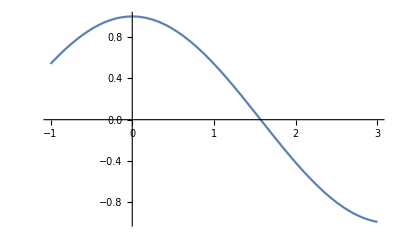

```mathematica
x0=Input["Enter first number"];
Nmax=Input["Enter the maximum value of iterations:"];
eps=Input["Enter the value of convergence paramaeter"];
Print["x0=",x0];
Print["Nmax=",Nmax];
Print["epsilon=",eps];
f[x_]:=Cos[x];
Print["f[x]:=",f[x]];
Print["f'[x]:=",D[f[x],x]];
For[i=1,i≤Nmax,i++,
x1=N[x0-(f[x]/.x->x0)/(D[f[x],x]/.x->x0)];
If[Abs[x1-x0]<eps,Return[x1],x0p=x0;x0=x1];
Print["In ", i,"th number of iteration the root is :",x1];
Print["estimated error is;",Abs[x1-x0p]]];
Print[" the Approximation of Root is" ,x1];
Print["estimated error is:",Abs[x1-x0]];
Plot[f[x],{x,-1,3}]
```

## Question 2

Perform the iteration to find the solution of the function f[x]=x^3-5x+1.then 
plot the graph of the iterations and then find the most error free answer of the
functions.

x0=1

Nmax=20

epsilon=1/1000000

f[x]:=1-5 x+x^3

f'[x]:=-5+3 x^2

In 1th number of iteration the root is :-0.5

estimated error is;1.5

In 2th number of iteration the root is :0.294118

estimated error is;0.794118

In 3th number of iteration the root is :0.200215

estimated error is;0.093903

In 4th number of iteration the root is :0.201639

estimated error is;0.00142474

Return[0.20164]

the Approximation of Root is0.20164

estimated error is:2.50538×10^-7

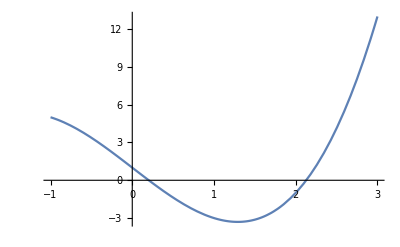

```mathematica
x0=Input["Enter first number"];
Nmax=Input["Enter the maximum value of iterations:"];
eps=Input["Enter the value of convergence paramaeter"];
Print["x0=",x0];
Print["Nmax=",Nmax];
Print["epsilon=",eps];
f[x_]:=x^3-5*x+1;
Print["f[x]:=",f[x]];
Print["f'[x]:=",D[f[x],x]];
For[i=1,i≤Nmax,i++,
x1=N[x0-(f[x]/.x->x0)/(D[f[x],x]/.x->x0)];
If[Abs[x1-x0]<eps,Return[x1],x0p=x0;x0=x1];
Print["In ", i,"th number of iteration the root is :",x1];
Print["estimated error is;",Abs[x1-x0p]]];
Print[" the Approximation of Root is" ,x1];
Print["estimated error is:",Abs[x1-x0]];
Plot[f[x],{x,-1,3}]
```

## Question 3

### Perform the iteration to find the solution of the function f[x]=cos[x]-xe^[x].then plot the graph of the iterations and then find the most error free answer of the functions.

x0=1

Nmax=20

epsilon=1/1000000

f[x]:=-ⅇ^x x+Cos[x]

f'[x]:=-ⅇ^x-ⅇ^x x-Sin[x]

In 1th number of iteration the root is :0.653079

estimated error is;0.346921

In 2th number of iteration the root is :0.531343

estimated error is;0.121736

In 3th number of iteration the root is :0.51791

estimated error is;0.0134335

In 4th number of iteration the root is :0.517757

estimated error is;0.00015253

Return[0.517757]

the Approximation of Root is0.517757

estimated error is:1.94824×10^-8

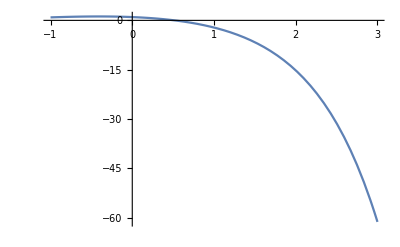

```mathematica
x0=Input["Enter first number"];
Nmax=Input["Enter the maximum value of iterations:"];
eps=Input["Enter the value of convergence paramaeter"];
Print["x0=",x0];
Print["Nmax=",Nmax];
Print["epsilon=",eps];
f[x_]:=Cos[x]-x*Exp[x];
Print["f[x]:=",f[x]];
Print["f'[x]:=",D[f[x],x]];
For[i=1,i≤Nmax,i++,
x1=N[x0-(f[x]/.x->x0)/(D[f[x],x]/.x->x0)];
If[Abs[x1-x0]<eps,Return[x1],x0p=x0;x0=x1];
Print["In ", i,"th number of iteration the root is :",x1];
Print["estimated error is;",Abs[x1-x0p]]];
Print[" the Approximation of Root is" ,x1];
Print["estimated error is:",Abs[x1-x0]];
Plot[f[x],{x,-1,3}]
```